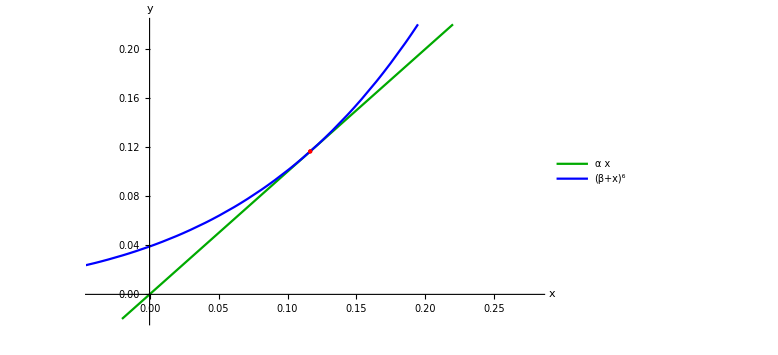

```mathematica
a=1;
b=0.582355932;
f[a_, x_]=a*x;
g[b_, x_]=(b+x)^6;
intersection ={x, f[a,x]}/. Solve[f[a,x]==g[b,x], x,Reals];
fg=Plot[
{f[a,x], g[b, x]}, 
{x, -1, 1}, 
PlotLegends->{α*x, (β+x)^6},
PlotRange->{{-0.04, 0.28}, {-0.02, 0.22}},
PlotStyle->{Darker[Green], Blue},
ImageSize->Large,
Epilog->{Red,PointSize[Large], Point[intersection]},
AxesLabel->{"x", "y"}
]
Export["C:\\Users\\user\\Desktop\\small.svg", fg];
Export["C:\\Users\\user\\Desktop\\big.svg",fg,ImageSize->2000,"CompressionLevel"->0];
```